# the workload test part 2

```mathematica
SetDirectory[NotebookDirectory[]];
rl[d_]:=Placed[d,Axis,Rotate[#,Pi/2]&]
SwapLoad[file_String]:=Import["../dataset/"<>file][[3;;All,5]]
VMLoad[file_String]:=Import["../dataset/"<>file][[4;;]];
```

## dynamic tau redo all test

### 3-8 dynamic tau

key | value | key | value
N | 5GB | init mem | 512MB
VM count | 10 | f | 150MB
high load | 200MB | □ | □

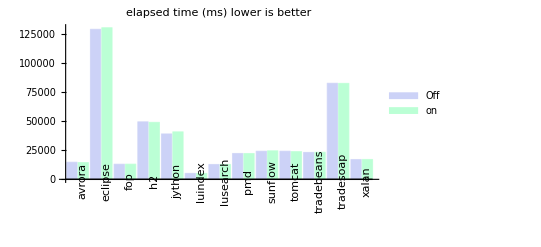

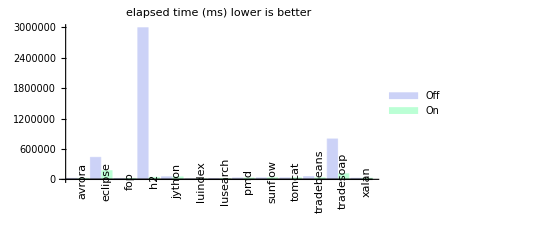

(ms) | off | on
avrora | 18238 | 17358
eclipse | 433186 | 171196
fop | 16029 | 17748
h2 | 2991145 | 37778
jython | 49847 | 47796
luindex | 6268 | 6144
lusearch | 15821 | 16029
pmd | 27475 | 26530
sunflow | 29067 | 30805
tomcat | 29034 | 29370
tradebeans | 54152 | 29416
tradesoap | 796455 | 110001
xalan | 21351 | 22948
sum | 4488068 | 563119

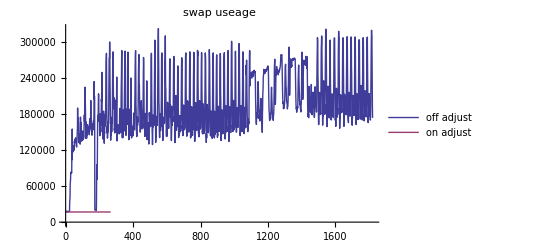

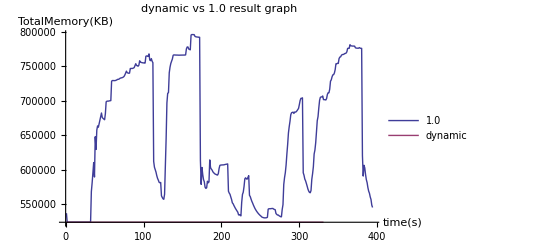

```mathematica
dp=Import["../dataset/3-8_dacapo/dacapo.ods"][[1]];
swapoff=SwapLoad["3-8_dacapo/off-swap.log"];
swapon=SwapLoad["3-8_dacapo/on-swap.log"];
hi=VMLoad["3-8_dacapo/high-2.log"];
low=VMLoad["3-8_dacapo/low-2.log"];
BarChart[dp[[2;;-2,2;;3]],
ChartLabels->{rl[dp[[2;;-2,1]]],None},
ChartLegends->{"Off","on"},PlotLabel->"elapsed time (ms) lower is better"]
BarChart[dp[[2;;-2,4;;5]],
ChartLabels->{rl[dp[[2;;-2,1]]],None},
ChartLegends->{"Off","On"},PlotLabel->"elapsed time (ms) lower is better"]
Grid[dp[[All,{1,4,5}]],Frame->All]
ListLinePlot[{swapoff,swapon},
PlotLabel->"swap useage",
PlotLegends->{"off adjust","on adjust"}]
ListLinePlot[{hi[[All,3]],low[[All,3]]},
PlotLegends->{"1.0","dynamic"},AxesLabel->{"time(s)","TotalMemory(KB)"},PlotLabel->"dynamic vs 1.0 result graph"]
Clear[dp,swapoff,swapon,hi,low]
```

配置512MB内存,运行时间相差非常大,而且几乎无法看到开启调节的柱状图.
而且SWAP分区使用率也是非常的夸张.
这个只能说是对于人而言.没有美观的感觉.但是对于系统而言是正常的结果.
我们需要接受它,当然.在论文中不使用这组数据.

### 3-9 dynamic tau high

key | value | key | value
N | 10GB | init mem | 1GB
VM count | 10 | f | 150MB
high load | 800MB | □ | □

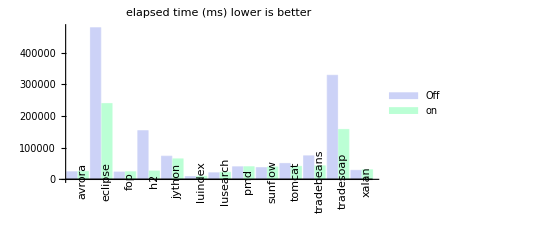

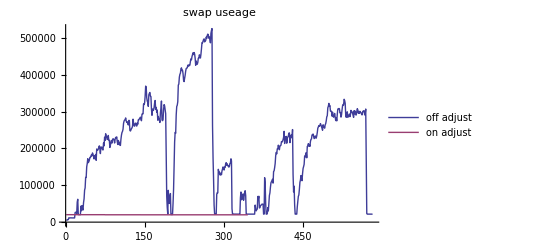

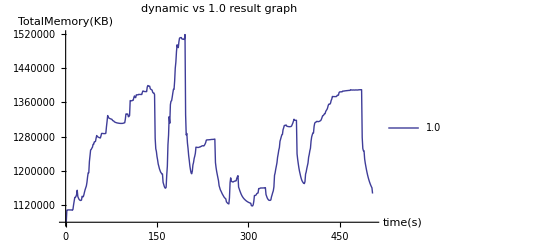

```mathematica
dp=Import["../dataset/3-9_dacapo_high/dacapo.ods"][[1]];
swapoff=SwapLoad["3-9_dacapo_high/off-swap.log"];
swapon=SwapLoad["3-9_dacapo_high/on-swap.log"];
hi=VMLoad["3-9_dacapo_high/high-10.log"];
BarChart[dp[[2;;-2,2;;3]],
ChartLabels->{rl[dp[[2;;-2,1]]],None},
ChartLegends->{"Off","on"},PlotLabel->"elapsed time (ms) lower is better"]
ListLinePlot[{swapoff,swapon},
PlotLabel->"swap useage",
PlotLegends->{"off adjust","on adjust"}]
ListLinePlot[{hi[[All,3]]},
PlotLegends->{"1.0","dynamic"},AxesLabel->{"time(s)","TotalMemory(KB)"},PlotLabel->"dynamic vs 1.0 result graph"]
Clear[dp,swapoff,swapon]
```

结论和以前的类似.